Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

March 1, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Analysis of LogS Values for 257 Known Drugs

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of February 17, 2011, we evaluated a dataset of 257 known drugs that contains the melting point, the logP, and the logS values for each of the compounds.

## Methodology

For this study, the list of 257 drugs was collected from the NCSSM Canvas website. The following analyses were conducted:

Drug data was imported into Mathematica

Data was summarized through descriptive statistics

The relationship between logP and logS was analyzed

The relationship between predicted logS and logS was analyzed

Data was filtered to find drugs with a logS above zero

### Data Import and Description:

```mathematica
drugData = Import["/Users/aakritilakshmanan/Downloads/drugGSEdata.csv"];
viableDrug=drugData;
drugData // TableForm
```

Name | MP | logP | logS
1,2,3-Trichlorobenzene | 52.6 | 3.8 | -3.76
1,3,5-Trichlorobenzene | 63.4 | 4.3 | -4.44
1,4-Dibromobenzene | 87.31 | 4.1 | -4.07
17Alpha-ethynylestradiol | 143.5 | 4.5 | -4.484
2-Naphthol | 122 | 2.7 | -2.159
3-Methylcholanthrene | 179.5 | 7.1 | -7.97
3,4-Benzopyrene | 179 | 6.5 | -7.82
4-Aminobenzoic acid | 187.75 | 0 | -1.368
5-Allyl-5-phenylbarbiturate | 158.5 | 2 | -2.346
5-Aminosalicylic acid | 280 | 0.5 | -2.259
5-Ethyl-5-(3-methylbut-2-enyl)barbiturate | 158.3 | 2 | -2.253
5-Ethyl-5-allylbarbiturate | 160.7 | 0.9 | -1.614
5-Ethyl-5-heptylbarbiturate | 118 | 3.3 | -3.218
5-Ethyl-5-nonylbarbiturate | 113 | 4.4 | -4.462
5-Ethyl-5-octylbarbiturate | 113 | 3.9 | -3.943
5-Ethyl-5-pentylbarbiturate | 135 | 2.3 | -2.34
5-Ethyl-5-propylbarbiturate | 144 | 1.2 | -1.491
5-Ethyl-barbiturate | 191 | -0.4 | -1.427
5-i-Propyl-5-(3-methylbut-2-enyl)barbiturate | 131.3 | 2.3 | -2.593
5-Methyl barbiturate | 220 | -0.9 | -1.126
5-Methyl-5-(3-methylbut-2-enyl)barbiturate | 193 | 1.5 | -2.602
5-Methyl-5-allylbarbiturate | 167 | 0.4 | -1.16
5-Methyl-5-ethylbarbiturate | 216 | 0.2 | -1.162
5-t-Butyl-5-(3-methylbut-2-enyl)barbiturate | 212 | 2.7 | -3.551
5,5-Di-i-propylbarbiturate | 227.5 | 1.4 | -2.766
5,5-Diethylbarbiturate | 190 | 0.7 | -1.41
5,5-Dimethylbarbiturate | 278 | -0.4 | -1.742
5,5-Diphenylbarbiturate | 288 | 2.6 | -4.196
5,5-Dipropylbarbiturate | 146.5 | 1.7 | -2.527
Acenaphthene | 95 | 4 | -4.59
Acetaminophen | 169.75 | 0.3 | -1.074
Acetanilide | 114 | 1.1 | -1.398
Acetazolamide | 258.5 | -0.3 | -2.489
Adenosine | 234.5 | -1.3 | -1.728
Alclofenac | 92.5 | 2.8 | -3.125
Allobarbital | 172 | 1.2 | -1.796
Aminopyrine | 108 | 0.8 | -0.619
Amobarbital | 157 | 2.1 | -2.47
Ampicillin | 200.5 | 1.4 | -1.539
Anthracene | 218 | 4.6 | -6.38
Antipyrine | 112 | 0.3 | 0.48
Aprobarbital | 142.7 | 1.3 | -1.71
Ascorbic acid | 191 | -2.4 | 0.277
Aspirin | 135 | 1.2 | -1.733
Atrazine | 172.5 | 1 | -3.489
Atropine | 115 | 1.5 | -2.124
Azathioprine | 243.5 | 0.9 | -3.443
Azintamide | 97.5 | 1.6 | -1.716
Aztreonam | 227 | -2.2 | -1.639
Benperidol | 170.9 | 3.7 | -4.28
Benzamide | 130 | 0.7 | -0.953
Benzanthracene | 160 | 5.9 | -7.21
Benzoic acid | 122.4 | 1.9 | -1.555
Betamethasone | 232.5 | 2.1 | -3.77
Bumetanide | 230.5 | 2.8 | -3.562
Busulfan | 116 | -0.5 | -2.267
Butalbital | 140 | 1.8 | -2.119
Butamben | 58 | 3.6 | -3.131
Butobarbitone (Butethal) | 125.5 | 1.7 | -1.686
Butylparaben | 68.5 | 3.5 | -3.101
Camphor | 179.8 | 2.1 | -2.086
Carbamazepine | 191.5 | 2.7 | -3.294
Carbofuran | 151.5 | 1.8 | -2.5
Cefazolin | 190 | 1.1 | -2.616
Ceftazidime | 136 | 0 | -2.038
Chloral hydrate | 57 | 1.7 | 1.7
Chloramphenicol | 151 | 1 | -2.111
Chlordiazepoxide | 236 | 1 | -2.176
Chlorpyrifos | 41.5 | 4.8 | -5.244
Chlortetracycline | 168.5 | 3.6 | -2.94
Chlorthalidone | 225 | -0.7 | -3.451
Chlorzoxazone | 191.75 | 2.2 | -2.831
Chrysene | 254 | 5 | -8.06
Cimetidine | 142 | 0.4 | -1.613
Clofazimine | 211 | 7.5 | -5.8
Cocaine | 98 | 3 | -2.26
Colchicine | 146 | 1 | -0.944
Corticosterone | 145 | 1.8 | -3.24
Cortisone | 222 | 1.2 | -3.27
Cyclobarbital | 172.5 | 2.1 | -2.273
Cyclobutane-spirobarbiturate | 271.5 | 0.1 | -2.349
Cycloethane-spirobarbiturate | 325 | -1 | -1.886
Cycloheptane-spirobarbiturate | 228 | 1.8 | -2.982
Cyclohexane-spirobarbiturate | 266 | 1.2 | -3.168
Cyclopentane-spirobarbiturate | 288 | 0.7 | -3.06
Cyclopropane-spirobarbiturate | 257 | -0.5 | -1.655
Cycloserine | 155.5 | -1.8 | -0.009
Cyproheptadine | 112.8 | 6.6 | -1.898
Danazol | 225.6 | 4.7 | -5.507
Danthron | 195 | 3.8 | -5.187
Dapsone | 175.5 | 0.9 | -3.094
Deoxycorticosterone | 141.5 | 3.4 | -3.45
Dexamethasone | 263 | 2.1 | -3.59
Diazepam | 125.5 | 3 | -3.754
Dichlorprop | 117.5 | 2.9 | -2.827
Diclofenac | 157 | 3.3 | -5.097
Didanosine | 161.5 | -1.3 | -0.937
Diflunisal | 210.5 | 4.3 | -4.479
Dihydroequilenin | 174.5 | 4 | -4.642
Dihydroequilin | 174 | 3.8 | -4.402
Dimorpholamine | 41.5 | -0.2 | 0.098
Diosgenin | 205.5 | 5.7 | -2.618
Diphenyl | 70 | 4 | -4.34
Disopyramide | 94.75 | 2.9 | -1.701
Disulfiram | 70 | 4 | -2.995
Diuron | 158.5 | 2.8 | -3.76
Dyphylline | 158 | -1.1 | 0.118
Epinephrine | 211.5 | -0.6 | -2.74
Equilenin | 258.5 | 3.8 | -5.249
Equilin | 239 | 3.5 | -5.282
Estradiol | 176 | 4.1 | -4.845
Estriol | 282 | 2.9 | -4.955
Estrone | 255.3 | 3.7 | -3.955
Ethambutol | 88.2 | -0.1 | -0.565
Ethyl-4-aminobenzoate (Benzocaine) | 89 | 2.5 | -2.616
Ethylparaben | 116 | 2.4 | -2.346
Etomidate | 67 | 3.4 | -6.735
Fenbuconazole | 125 | 3.9 | -6.226
Fenbufen | 186 | 3 | -5.301
Fenchlorphos | 41 | 4.8 | -3.905
Fenclofenac | 135 | 4.9 | -3.854
Fenoxycarb | 53.5 | 3.8 | -4.719
Fenpiclonil | 152.9 | 2.7 | -5.074
Flucytosine | 296 | -1.8 | -0.959
Fludioxonil | 199.4 | 0.4 | -5.21
Fludrocortisone | 261 | 1.3 | -3.434
Flufenamic acid | 125 | 5.6 | -4.623
Fluometuron | 163.5 | 2.4 | -3.463
Fluorene | 116.5 | 4.5 | -4.92
Fluorouracil | 282 | -0.8 | -1.028
Flurbiprofen | 110 | 4.1 | -3.74
G-BHC (Lindane) | 112.5 | 3.9 | -4.6
Glafenine | 169.5 | 3.9 | -4.571
Glutethimide | 87.5 | 2.7 | -2.337
Griseofulvin | 220 | 2.4 | -3.246
Guaifenesin | 78.75 | 0.6 | -0.598
Haloperidol | 148.7 | 4.1 | -4.429
Heptabarbital | 175 | 2.7 | -3
Heptobarbital | 228.5 | 1.2 | -2.38
Heroin | 173 | 2.1 | -2.798
Hexachlorobenzene | 231 | 6.5 | -7.76
Hexethal | 125 | 2.8 | -3.049
Hydrochlorothiazide | 274 | -0.1 | -2.689
Hydrocortisone | 218.5 | 1.4 | -3.1
Hydroflumethiazide | 272.5 | 0.5 | -3.043
Hyoscyamine | 108.5 | 1.5 | -1.91
Ibuprofen | 76 | 3.7 | -3.42
Idobutal | 128 | 2 | -2.172
Indapamide | 161 | 2.1 | -3.792
Indoprofen | 213.5 | 1.7 | -4.824
Iodamide | 256 | 0.1 | -2.321
Iopanoic acid | 156.1 | 5.2 | -4.58
Iprodione | 136 | 1.8 | -4.405
Isocarboxazid | 105.5 | 1 | -2.461
Isoniazid | 171.4 | -0.9 | 0.009
Isopropylbarbiturate | 216 | 0 | -1.456
Isoproturon | 158 | 2.3 | -3.469
Ketoprofen | 94 | 2.8 | -3.155
Khellin | 154.5 | 1.7 | -3.017
L-DOPA | 277 | -0.2 | -1.818
Lidocaine | 68.5 | 2.4 | -1.768
Linuron | 93.5 | 3.2 | -3.521
Lomefloxacin | 239.75 | 2.4 | -2.533
Lorazepam | 167 | 2.5 | -3.604
Lovastatin | 174.5 | 4.1 | -6
Mefenamic acid | 230.5 | 5.3 | -3.77
Melphalan | 182.5 | 2.4 | -3.485
Meprobamate | 105 | 0.7 | -1.807
Methaqualone | 120 | 2.7 | -2.921
Methocarbamol | 93 | 0.5 | -0.985
Methyclothiazide | 225 | 1.8 | -3.778
Methyl-p-hydroxybenzoate | 131 | 1.9 | -1.705
Methyltestosterone | 163.5 | 4 | -3.99
Methyprylon | 75.5 | 0.2 | -0.382
Metoclopramide | 147.25 | 2.3 | -3.176
Metronidazole | 159 | 0 | -1.212
Minoxidil | 248 | -1.5 | -1.978
Mitomycin C | 360 | 0.1 | -2.564
Morphine | 254 | 1 | -3.154
Nadolol | 125 | 1.3 | -1.008
Nalidixic acid | 229.5 | 0.2 | -3.366
Naphthacene | 357 | 5.9 | -8.69
Naphthalene | 80.2 | 3.4 | -3.61
Naproxen | 153 | 3 | -4.155
Nicotinamide | 129.5 | -0.1 | 0.913
Nicotinic acid | 236.6 | 0.8 | -0.85
Norethisterone | 203.5 | 3.4 | -4.63
Norfloxacin | 220.5 | 1.5 | -3.057
Oxamniquine | 148 | 1.5 | -2.965
Oxazepam | 205.5 | 2.3 | -3.952
p-Aminosalicylic acid | 150.5 | 0.3 | -1.963
Penicillamine | 204 | 0.9 | -0.128
Pentazocin | 146 | 5.3 | -3.803
Pentobarbital | 129.5 | 2.1 | -2.41
Pentoxifylline | 105 | 0.4 | -0.558
Perphenazine | 97 | 4.5 | -4.155
Perylene | 273.5 | 6.5 | -8.8
Phenacetin | 134.5 | 1.6 | -2.371
Phenanthrene | 100 | 4.6 | -5.15
Phenobarbital | 175 | 1.7 | -2.366
Phenolphthalein | 260 | 3.3 | -2.9
Phenylbutazone | 105 | 3.5 | -2.644
Phenytoin | 296.5 | 2.5 | -4.226
Prasterone | 140.5 | 3.4 | -4.064
Praziquantel | 137 | 3.6 | -2.893
Primidone | 281.5 | -1 | -2.64
Probarbital | 198 | 1 | -2.153
Progesterone | 126 | 4 | -4.42
Proline | 221 | -0.6 | 1.149
Promethazine | 60 | 4.7 | -4.26
Propoxur | 91.5 | 1.6 | -2.02
Propranolol | 96 | 3.1 | -0.714
Propylparaben | 96.5 | 2.9 | -2.557
Propylthiouracil | 220 | 1.4 | -2.185
Prostaglandin E2 | 67 | 2.2 | -2.47
Proxyphlline | 135.5 | -0.2 | 0.623
Pyrazinamide | 190 | -0.4 | -0.914
Pyrene | 156 | 5.2 | -6.18
Quinidine | 174.5 | 3.4 | -2.812
Quinine | 177 | 3.4 | -2.79
Reposal | 213 | 2.5 | -2.773
Saccharin | 229.25 | 0.9 | -1.725
Salicylamide | 140 | 1.4 | -1.836
Salicylic acid | 158 | 2.1 | -1.804
Secbutabarbital | 166.5 | 1.6 | -2.333
Secobarbital | 95 | 2.3 | -2.333
Simvastatin | 136.5 | 4.4 | -4.145
Sorbitol | 111 | -5 | 1.148
Stanolone | 181 | 3.8 | -4.743
Strychnine | 280 | 1.7 | -3.33
Sulfacetamide | 183 | -0.9 | -1.507
Sulfadiazine | 252.5 | -0.1 | -3.529
Sulfamerazine | 236.5 | 0.3 | -1.218
Sulfamethazine | 176 | 0.8 | -2.268
Sulfamethoxazole | 171.5 | 0.9 | -2.705
Sulfanilamide | 165.5 | -0.7 | -1.361
Sulfathiazole | 202 | 0.3 | -2.805
Sulindac | 183.5 | 3.6 | -5
Sulpiride | 179 | 0.5 | -2.876
Talbutal | 109 | 1.8 | -2.016
Tenoxicam | 211 | -0.3 | -3.875
Terfenadine | 147.5 | 6.9 | -4.674
Testosterone | 155 | 3.5 | -4.07
Tetroxoprim | 154.5 | 0.5 | -2.101
Thalidomide | 270 | 0.5 | -3.699
Thebaine | 193 | 4.6 | -2.658
Thiamphenicol | 165.3 | -0.3 | -2.154
Thioridazine | 73 | 6.1 | -5.824
Triamcinolone | 270 | 1.1 | -3.693
Triazolam | 234 | 2.7 | -4.09
Trimethoprim | 201 | 0.8 | -2.861
Triphenylene | 199 | 5.5 | -6.73
Tropicamide | 98 | 1.2 | -1.698
Tybamate | 51.5 | 2.9 | -2.739
Vinbarbital | 165 | 1.8 | -2.458
Zidovudine | 109 | -0.6 | -1.029
Zileuton | 157.5 | 2.9 | -3.373

## Results

### Descriptive Statistics

We determined the mean, median, standard deviation, and quartiles for our data set, and produced a box/whisker plot for each of the three variables. As can be seen in the box whisker plots below, most of the molecules examined have a melting point between 122 and 214 degrees. Melting point has the highest standard deviation out of the other variable examined, which means that there is more variance in the meting point values. In contrast, logP and logS are found within a much smaller range of values. In addition, the standard deviation is lower, which means that most of the compounds examined have similar logP and logS values. The logP dataset has a very close mean and median, which means that the logP data values are quite centered around the value of 2.

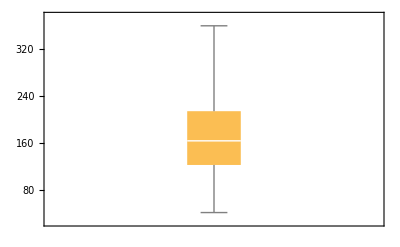
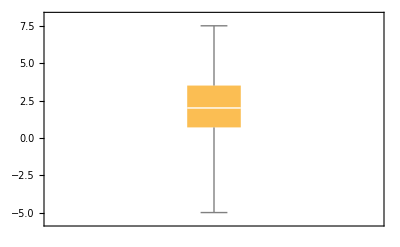
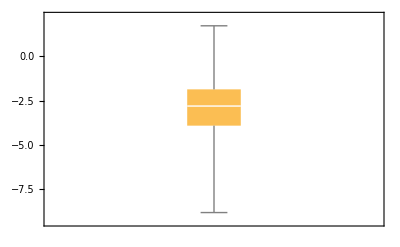
| MP | logP | logS
Mean | 168.28 | 2.08482 | -2.96464
Median | 163.5 | 2 | -2.812
Standard Deviation | 63.2095 | 1.96114 | 1.70755
Quartiles | {122.3,163.5,214.125} | {0.7,2,3.5} | {-3.9145,-2.812,-1.8735}
BoxWhisker Plot | -Graphics- | -Graphics- | -Graphics-

```mathematica
header = drugData[[1]];
drugData = Delete[drugData,1];
{name, mp, logP, logS} = Transpose[drugData];
descriptiveStats = Grid[{{"", header[[2]], header[[3]], header[[4]]}, {"Mean", Mean[mp], Mean[logP], Mean[logS]}, {"Median", Median[mp], Median[logP], Median[logS]}, {"Standard Deviation", StandardDeviation[mp], StandardDeviation[logP], StandardDeviation[logS]}, {"Quartiles", Quartiles[mp], Quartiles[logP], Quartiles[logS]}, {"BoxWhisker Plot", BoxWhiskerChart[v=mp], BoxWhiskerChart[logP], BoxWhiskerChart[logS]}}, Frame -> All]
```

### Plot of Results

#### Data Analysis of logP and logS

We prepared a plot of logP versus logS, as shown below. Based on this plot, we can see that there is a negative relationship between logP and logS. The line of best fit has a R squared of value of - .75, meaning that there is a quantifiable correlation between these two variables. However, this relationship is not extremely strong since the R squared value could be closer to one. Therefore it can be hypothesized that there remains another variable that also plays a role in logS in addition to logP. The line of best fit (shown in “normal” model), where x is logP, is:

```mathematica
logTogether = Transpose[{logP,logS}];
myFit = LinearModelFit[logTogether, x,x];  
Normal[myFit];
Print["logS =", TraditionalForm[Normal[myFit]]]
rval1=Correlation[logP,logS];
```

logS =-0.656499 x-1.59596

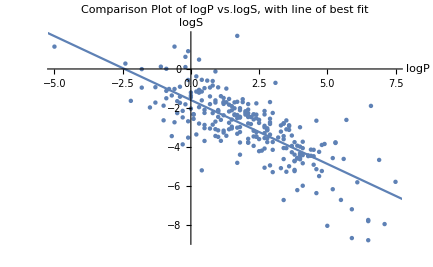

```mathematica
dataPlot = ListPlot[logTogether, AxesLabel->{"logP","logS"},PlotLabel->"Comparison Plot of logP vs.logS, with line of best fit",LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}];
fitPlot = Plot[myFit[x],{x,-100,100}];
Show[ dataPlot,fitPlot]
```

#### Data Analysis of logS and predicted logS

We prepared a plot of logS versus predicted logS, as shown below. Based on this plot, we can see that the empirical function for logS, known as the General Solubility Equation, is very correlated to the experimental logS values. The plotted line of best fit has an R squared value of  .81, which shows that there is a strong positive relationship between these two values. Compared to above, the R squared value has been increased by taking into account the melting point in addition to the logP value. Despite outliers that can be seen on this graph, overall, it can be concluded that the General Solubility Equation efficiently and accurately models the logS value of the selected compounds.

```mathematica
myFunction[x_,y_]= 0.8 - x- 0.01(y-25);
predictedLogS = List[];
For[i=1,i<(Length[logP]+1),i++,AppendTo[predictedLogS,myFunction[logP[[i]],mp[[i]]]]];
```

```mathematica
logSTogether = Transpose[{logS,predictedLogS}];
myLogSFit = LinearModelFit[logSTogether, x,x];  
Normal[myLogSFit];
Print["Predicted logS =", TraditionalForm[Normal[myLogSFit]]]
rval2=Correlation[logS,predictedLogS];
```

The line of best fit (shown in “normal” model), where x is logS, is:

Predicted logS =0.917945 x+0.00375459

```mathematica
datalogSPlot = ListPlot[logSTogether, AxesLabel->{"logS","Predicted logS"},PlotLabel->"Comparison Plot of logS vs. predicted logS, with line of best fit",LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}];
fitlogSPlot = Plot[myLogSFit[x],{x,-10,4}];
Show[ datalogSPlot,fitlogSPlot]
```

A graph of logS vs. predicted logS is shown below, with the line of best fit superimposed over the data:

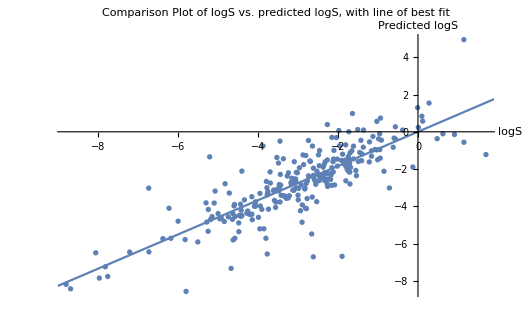

#### Determination of logS>0 drugs

We filtered the data to show which of the 257 drugs in our dataset have a logS value of greater than 0. Of the 257 drugs, we found 10 drugs with a logS value > 0. Drugs with a logS value over 0 are ranked 5 on the solubility ranking, and are too soluble for use as drugs within the body. As such, the following drugs can be filtered out and rejected before further analysis. These drugs are shown below:

```mathematica
Grid[
Map[
{
#[[1]],
#[[2]],
#[[3]],
#[[4]]
} &,
DeleteCases[viableDrug, a_ /; a[[4]] < 0]
],
Frame -> All]
```

Name | MP | logP | logS
Antipyrine | 112 | 0.3 | 0.48
Ascorbic acid | 191 | -2.4 | 0.277
Chloral hydrate | 57 | 1.7 | 1.7
Dimorpholamine | 41.5 | -0.2 | 0.098
Dyphylline | 158 | -1.1 | 0.118
Isoniazid | 171.4 | -0.9 | 0.009
Nicotinamide | 129.5 | -0.1 | 0.913
Proline | 221 | -0.6 | 1.149
Proxyphlline | 135.5 | -0.2 | 0.623
Sorbitol | 111 | -5 | 1.148

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on March 1, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References: